```mathematica
SetOptions[EvaluationNotebook[],CellContext->Notebook]
```

```mathematica
f[r_]:=1-1/r
```

```mathematica
g[r_]:=1/f[r]
```

```mathematica
V[r_,b_]:=-(1/2)*(f[r]/g[r])*(1-b^2*f[r]/r^2)//Simplify
```

```mathematica
a[r_,b_]:=-D[V[r,b],r]//Simplify
```

```mathematica
Solve[V[r,19.967]==0,r]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{r→-20.4494},{r→1.},{r→1.},{r→1.00253},{r→19.4469}}

```mathematica
s=NDSolve[{r''[t]==a[r[t],19.967],r[0]==100,r'[0]==-0.9703},r,{t,0,200}]
```

{{r→InterpolatingFunction[{{0.,200.}},<>]}}

```mathematica
{{r->InterpolatingFunction[{{0.,200.}},"<>"]}}
```

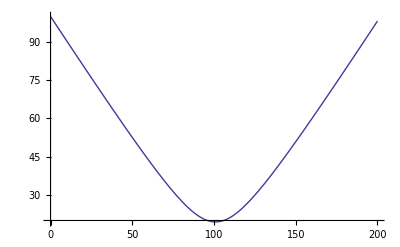

```mathematica
Plot[Evaluate[r[t]/.s],{t,0,200}]
```

```mathematica
Minimize[{rSol[t],90<t<110},t]
```

NMinimize::nnum: The function value {28.4653} is not a number at {t} = {90.9146}.

Minimize[{{InterpolatingFunction[{{0.,200.}},<>][t]},90<t<110},t]

```mathematica
rSol[t_]:=Evaluate[r[t]/.s]
```

```mathematica
rSol[t]
```

{InterpolatingFunction[{{0.,200.}},<>][t]}